#### Dear Wolfram Recruiters and Managers,

Thank you for your time and consideration in analyzing the following code and considering me for a position at Wolfram Research. The challenges were engaging and I had a blast completing them. For the most part, I managed to make practicable functions even where pseudocode was all that was required. In any event, I very much hope to hear from you soon!
										Regards,
										Kyle Wardlow

## Challenge 1

Given a function f(x), determine if it can be written in the form a*Sin[b x + c] + d. If so return the period, phase shift, amplitude, and midline. (These terms are defined here.)

More explicitally, write a function called TrigProperties that takes in a function (f) and a variable (x).

This function returns $Failed if f cannot be expressed in the form a*Sin[b x + c] + d, otherwise it returns

```mathematica
{"Period"->per,"Amplitude"->am,"PhaseShift"->ph,"Midline"->md}
```

Examples:

```mathematica
TrigProperties[x^2+1,x]
```

$Failed

```mathematica
TrigProperties[2Sin[x-π/12]+5,x]
```

{Period→2 π,Amplitude→-2,PhaseShift→π/12,Midline→5}

```mathematica
TrigProperties[Cos[x]^2,x]
```

{Period→π,Amplitude→1/2,PhaseShift→-π/4,Midline→1/2}

### Operational Function

```mathematica
(*Here is the operational TrigProperties Function*)
TrigProperties[functionInput_,variableInput_]:=(
(*First, we handle the case of constants.*)
SimplifiedFunction=FullSimplify[functionInput];

If[NumberQ[SimplifiedFunction],
{"Period"->"N/A","Amplitude"->0,"PhaseShift"->"N/A","Midline"->SimplifiedFunction},

(*Second, we need to deal with functions that have poles/divergences. These cannot be represented in the above fashion and so we can eliminate potentially problematic input by filtering for these first.*)
If[Resolve[Exists[variableInput,1/functionInput==0]],
$Failed,
(*The next class of disqualified functions are any that go to ±∞ as x-> ±∞. Mostly here we're weeding out polynomials and other divergent functions missed by the first filter because of ∞.*)
If[ContainsAny[Limit[functionInput,variableInput->#]&/@{-∞,∞},{-∞,∞}],
$Failed,
(*Once these disqualified functions have been removed, we must determine if the function has any part which does not arise from a purely trigonometric function. Functions composed of sines and cosines will break down into a weighted sum of δ functions; we can filter out anything that does not look like this.*)
FourieredFunctionList=Apply[List,Collect[FourierTransform[FullSimplify[functionInput],variableInput,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]];

If[Cases[FourieredFunctionList,Except[_.*DiracDelta[_.+ω]]]≠{},$Failed,
(*Now that we have weeded out anything that does not decompose into sines/cosines, we go about the final task of using the spectrum given by the Fourier analysis (i.e. the arguments of the δ functions) to determine whether or not the input can be represented as one sine function. We only need to count how many terms are in the resulting transform to determine this.*)

SpectralAnalyzer=DeleteCases[Cases[Level[FourieredFunctionList,3],_+ω|ω]-ω,0];
If[Length[SpectralAnalyzer]>2,$Failed,

If[NumericQ[First[Level[FourieredFunctionList,2]]],
ph=-Arg[Level[FourieredFunctionList,2][[1]]]+π/2;,
ph=-Arg[1]+π/2;
];
am=1/2(MaxValue[functionInput,variableInput]-MinValue[functionInput,variableInput]);
md=1/2(MaxValue[functionInput,variableInput]+MinValue[functionInput,variableInput]);
per=FunctionPeriod[functionInput,variableInput];

{"Period"->per,"Amplitude"->am,"PhaseShift"->ph,"Midline"->md}
]
]
]
]
]
);
```

### Brainstorm

```mathematica
(*The function must be able to take any functional input and test whether or not it can be represented as a*Sin[b x+c]+d. One way of doing this would be to Fourier transform the function
and determine how many frequency components there are. If the transform returns more that one non-zero Fourier mode, then the function cannot be represented in the above form and so should return $Failed. The problem with this is of course with functions that diverge as they approach ±∞. The native FourierTransform function times out and will not evaluate in a timely fashion, so we have to first eliminate functions that have singularities. Naturally, these functions cannot be represented as a*Sin[b x+c]+d, so this will be our first filter. 

*)
```

### Function Development & Testing

```mathematica
(*Building TrigProperties functionality and testing the function against various permutations and representations of sinusoidal functions*)
```

```mathematica
(*Here is the operation TrigProperties Function*)
TrigProperties[functionInput_,variableInput_]:=(
(*First, we handle the case of constants.*)
SimplifiedFunction=FullSimplify[functionInput];

If[NumberQ[SimplifiedFunction],
{"Period"->"N/A","Amplitude"->0,"PhaseShift"->"N/A","Midline"->SimplifiedFunction},

(*Second, we need to deal with functions that have poles/divergences. These cannot be represented in the above fashion and so we can eliminate potentially problematic input by filtering for these first.*)
If[Resolve[Exists[variableInput,1/functionInput==0]],
$Failed,
(*The next class of disqualified functions are any that go to ±∞ as x-> ±∞. Mostly here we're weeding out polynomials and other divergent functions missed by the first filter because of ∞.*)
If[ContainsAny[Limit[functionInput,variableInput->#]&/@{-∞,∞},{-∞,∞}],
$Failed,
(*Once these disqualified functions have been removed, we must determine if the function has any part which does not arise from a purely trigonometric function. Functions composed of sines and cosines will break down into a weighted sum of δ functions; we can filter out anything that does not look like this.*)
FourieredFunctionList=Apply[List,Collect[FourierTransform[FullSimplify[functionInput],variableInput,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]];

If[Cases[FourieredFunctionList,Except[_.*DiracDelta[_.+ω]]]≠{},$Failed,
(*Now that we have weeded out anything that does not decompose into sines/cosines, we go about the final task of using the spectrum given by the Fourier analysis (i.e. the arguments of the δ functions) to determine whether or not the input can be represented as one sine function. We only need to count how many terms are in the resulting transform to determine this.*)

SpectralAnalyzer=DeleteCases[Cases[Level[FourieredFunctionList,3],_+ω|ω]-ω,0];
If[Length[SpectralAnalyzer]>2,$Failed,

If[NumericQ[First[Level[FourieredFunctionList,2]]],
ph=-Arg[Level[FourieredFunctionList,2][[1]]]+π/2;,
ph=-Arg[1]+π/2;
];
am=1/2(MaxValue[functionInput,variableInput]-MinValue[functionInput,variableInput]);
md=1/2(MaxValue[functionInput,variableInput]+MinValue[functionInput,variableInput]);
per=FunctionPeriod[functionInput,variableInput];



{"Period"->per,"Amplitude"->am,"PhaseShift"->ph,"Midline"->md}
]
]
]
]
]
);
```

```mathematica
TrigProperties[Tan[x],x]
TrigProperties[x,x]
TrigProperties[BesselJ[2,x],x]
TrigProperties[4,x]
TrigProperties[Sin[x],x]
TrigProperties[Cos[x],x]
TrigProperties[Sin[x]^3,x]
TrigProperties[Sin[x]^2,x]
TrigProperties[Sin[x]+Cos[4x],x]
TrigProperties[LegendreP[1,Cos[x]],x]
TrigProperties[4 Sin[x]^2+3 Sin[x]^2+7 Cos[x]^2,x]
TrigProperties[Exp[I π]-1,x]
```

$Failed

$Failed

$Failed

{Period→N/A,Amplitude→0,PhaseShift→N/A,Midline→4}

{Period→2 π,Amplitude→1,PhaseShift→0,Midline→0}

{Period→2 π,Amplitude→1,PhaseShift→π/2,Midline→0}

$Failed

{Period→π,Amplitude→1/2,PhaseShift→-π/2,Midline→1/2}

$Failed

{Period→2 π,Amplitude→1,PhaseShift→π/2,Midline→0}

{Period→N/A,Amplitude→0,PhaseShift→N/A,Midline→7}

{Period→N/A,Amplitude→0,PhaseShift→N/A,Midline→-2}

```mathematica
Abs[#[[1]]-ω]&/@(Apply[List,If[MatchQ[#,FourierOutputPattern],#[[2]]]&/@(1/4 DiracDelta[-4+ω]+1/4 DiracDelta[-3+ω]-1/4 DiracDelta[-6+ω]+DiracDelta[ω]/2-1/4 DiracDelta[6+ω])])
```

{6,4,3,0,6}

```mathematica
Gather[Abs[#[[1]]-ω]&/@(Apply[List,If[MatchQ[#,FourierOutputPattern],#[[2]]]&/@(FourierTransform[Sin[2x]+Sin[3x]+1,x,ω,FourierParameters->{-1, 1}])])]
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

{{Abs[-ω+Null⟦1⟧]},{3,3},{2,2}}

```mathematica
(Apply[List,If[MatchQ[#,FourierOutputPattern],#[[2]]]&/@(FourierTransform[Sin[2x]+Sin[3x]+1,x,ω,FourierParameters->{-1, 1}])])
```

{Null,DiracDelta[-3+ω],DiracDelta[-2+ω],DiracDelta[2+ω],DiracDelta[3+ω]}

```mathematica
(Apply[List,If[MatchQ[#,FourierOutputPattern],#[[2]]]&/@(FourierTransform[Sin[2x]+Sin[3x],x,ω,FourierParameters->{-1, 1}])])
```

{DiracDelta[-3+ω],DiracDelta[-2+ω],DiracDelta[2+ω],DiracDelta[3+ω]}

```mathematica
Cases[Level[{1/2 ⅈ DiracDelta[-3+ω],1/2 ⅈ DiracDelta[-2+ω],DiracDelta[ω],-1/2 ⅈ DiracDelta[2+ω],-1/2 ⅈ DiracDelta[3+ω]},3],_+ω|ω]
```

{-3+ω,-2+ω,ω,2+ω,3+ω}

```mathematica
Apply[List,FourierTransform[Sin[-2x]+Sin[3x]+1,x,ω,FourierParameters->{-1, 1}]]
Level[Apply[List,FourierTransform[Sin[-2x]+Sin[3x]+1,x,ω,FourierParameters->{-1, 1}]],3]
```

{1/2 ⅈ DiracDelta[-3+ω],-1/2 ⅈ DiracDelta[-2+ω],DiracDelta[ω],1/2 ⅈ DiracDelta[2+ω],-1/2 ⅈ DiracDelta[3+ω]}

{ⅈ/2,-3+ω,DiracDelta[-3+ω],1/2 ⅈ DiracDelta[-3+ω],-ⅈ/2,-2+ω,DiracDelta[-2+ω],-1/2 ⅈ DiracDelta[-2+ω],ω,DiracDelta[ω],ⅈ/2,2+ω,DiracDelta[2+ω],1/2 ⅈ DiracDelta[2+ω],-ⅈ/2,3+ω,DiracDelta[3+ω],-1/2 ⅈ DiracDelta[3+ω]}

```mathematica
Apply[List,FourierTransform[BesselJ[1,x]+1,x,ω,FourierParameters->{-1, 1}]]
Level[Apply[List,FourierTransform[BesselJ[1,x]+1,x,ω,FourierParameters->{-1, 1}]],2]
Cases[Level[Apply[List,FourierTransform[BesselJ[1,x]+1,x,ω,FourierParameters->{-1, 1}]],3],_+ω|ω]
DeleteCases[Cases[Level[Apply[List,FourierTransform[BesselJ[1,x]+1,x,ω,FourierParameters->{-1, 1}]],2],_+ω|ω]-ω,0]
```

{DiracDelta[ω],(ⅈ ω (-HeavisideTheta[-1+ω]+HeavisideTheta[1+ω]))/(π √(1-ω^2))}

{ω,DiracDelta[ω],ⅈ,1/π,ω,1/(√(1-ω^2)),-HeavisideTheta[-1+ω]+HeavisideTheta[1+ω],(ⅈ ω (-HeavisideTheta[-1+ω]+HeavisideTheta[1+ω]))/(π √(1-ω^2))}

{ω,ω}

{}

```mathematica
(*Not working for other special functions. Must isolation Dirac deltas as they contain the info on the pure freq spectrum of the original function.*)
```

```mathematica
Level[Apply[List,FourierTransform[2Cos[-2x]+1,x,ω,FourierParameters->{-1, 1}]],2]
Cases[Level[Apply[List,FourierTransform[Sin[-2x]+Sin[3x]+1,x,ω,FourierParameters->{-1, 1}]],2],DiracDelta[_]]
```

{-2+ω,DiracDelta[-2+ω],ω,DiracDelta[ω],2+ω,DiracDelta[2+ω]}

{DiracDelta[-3+ω],DiracDelta[-2+ω],DiracDelta[ω],DiracDelta[2+ω],DiracDelta[3+ω]}

```mathematica
{DiracDelta[-3+ω],DiracDelta[-2+ω],DiracDelta[ω],DiracDelta[2+ω],DiracDelta[3+ω]}
(*Check, Dirac δ's isolated*)
```

```mathematica
(*Try on Bessel functions again*)
(*Need to take care of false $Failed calls, so we need to reject ANY function that has anything but DiracDelta's in the Fourier transform.*)

Cases[Apply[List,FourierTransform[Sin[-2x]+Sin[3x]+1,x,ω,FourierParameters->{1, 1}]],Except[_.*DiracDelta[_]]]=={}


Cases[Apply[List,FourierTransform[BesselJ[2,x]+1,x,ω,FourierParameters->{1, 1}]],Except[_.*DiracDelta[_]]]=={}
```

True

False

```mathematica
DeleteCases[Cases[Level[Apply[List,FourierTransform[Sin[3x]+Cos[3x]+Cos[6x]^4,x,ω,FourierParameters->{-1, 1}]],3],_+ω|ω]-ω,0]
```

{-24,-12,-3,3,12,24}

```mathematica
(*This condition should suffice as the next level of filter*)
```

```mathematica
FourierTransform[Sin[2x]+Sin[3x],x,ω,FourierParameters->{-1, 1}]
FourierTransform[Sin[2x]+Sin[3x],x,ω]
```

1/2 ⅈ DiracDelta[-3+ω]+1/2 ⅈ DiracDelta[-2+ω]-1/2 ⅈ DiracDelta[2+ω]-1/2 ⅈ DiracDelta[3+ω]

ⅈ √(π/2) DiracDelta[-3+ω]+ⅈ √(π/2) DiracDelta[-2+ω]-ⅈ √(π/2) DiracDelta[2+ω]-ⅈ √(π/2) DiracDelta[3+ω]

```mathematica
#&/@(Apply[List,If[MatchQ[#,FourierOutputPattern],#[[2]]]&/@(-1/4 DiracDelta[-6+ω]+DiracDelta[ω]/2-1/4 DiracDelta[6+ω])])
```

{DiracDelta[-6+ω],DiracDelta[ω],DiracDelta[6+ω]}

```mathematica
FunctionPeriod[Sin[x]^3,x]
```

```mathematica
Resolve[Exists[x,1/Sin[x]^3==0]]
```

False

```mathematica
If[ContainsAny[Limit[x^3,x->#]&/@{-∞,∞},{-∞,∞}],$Failed,
```

```mathematica
ContainsAny[Limit[x^3,x->#]&/@{-∞,∞},{-∞,∞}]
ContainsAny[Limit[Sin[x],x->#]&/@{-∞,∞},{-∞,∞}]
```

True

False

```mathematica
md=1/2(MaxValue[Cos[4x]^2,x]+MinValue[Cos[4x]^2,x])
```

1/2

```mathematica
FunctionPeriod[Cos[4x]^2,x]
```

π/4

```mathematica
NSolve[Cos[4x]^2-1/2==0,x,x≤π/4]
```

NSolve::bdomv: Warning: x≤π/4 is not a valid domain specification. Assuming it is a variable to eliminate.

NSolve::ivar: x≤π/4 is not a valid variable.

```mathematica
Solve[ForAll[x,0≤x≤π/4,-1/2+Cos[4 x]^2==0],x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

{x→0.19635}

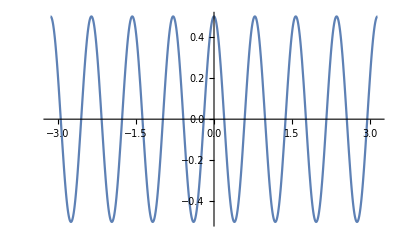

```mathematica
FindRoot[-1/2+Cos[4 x]^2,{x,0.01}]
Plot[-1/2+Cos[4 x]^2,{x,-π,π}]
```

```mathematica
TrigReduce[Cos[4 x-π/16]^2]
```

```mathematica
1/2 (1-Sin[8 x-π/8])
```

```mathematica
FindInstance[Cos[4*0.2+π]^2==1/2-1/2Sin[8*0.2+ϕ]&&Cos[4*(-0.1)+π]^2==1/2-1/2Sin[8*(-0.1)+ϕ],ϕ,Reals]
```

{}

```mathematica
FourierTransform[Cos[x/2]^2,x,ω,FourierParameters->{-1, 1}]
```

1/4 DiracDelta[-1+ω]+DiracDelta[ω]/2+1/4 DiracDelta[1+ω]

```mathematica
FourierTransform[Sin[x],x,ω,FourierParameters->{-1, 1}]
Collect[FourierTransform[Sin[x+π/6],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]
```

1/2 ⅈ DiracDelta[-1+ω]-1/2 ⅈ DiracDelta[1+ω]

(1/4+(ⅈ √3)/4) DiracDelta[-1+ω]+(1/4-(ⅈ √3)/4) DiracDelta[1+ω]

```mathematica
Arg[(1/4+(ⅈ √3)/4)]
```

π/3

```mathematica
ExpToTrig[Exp[I(x+π/6)]]
```

Cos[π/6+x]+ⅈ Sin[π/6+x]

```mathematica
F[ω]=∫Sin[x+π/6]*Exp[I ω x]ⅆx
F[ω]=∫(Exp[I(x+π/6)]-Exp[-I(x+π/6)])/(2I)*Exp[I ω x]ⅆx
```

```mathematica
Collect[Expand[(Exp[I(x+π/6)]-Exp[-I(x+π/6)])/(2I)*Exp[I ω x]],I]
```

1/2 ⅈ ⅇ^(-ⅈ (π/6+x)+ⅈ x ω)-1/2 ⅈ ⅇ^(ⅈ (π/6+x)+ⅈ x ω)

```mathematica
ExpToTrig[(Exp[I(x+π/6)]-Exp[-I(x+π/6)])/(2I)]
```

Sin[π/6+x]

```mathematica
1/2 I Exp[-I π/6]Exp[I x( ω-1)]-> I/2 Exp[-I π/6]DiracDelta[ω-1];

1/2 Exp[π/2] Exp[-I π/6]Exp[I x( ω-1)]-> 1/2 Exp[I π/2]Exp[-I π/6]DiracDelta[ω-1];
```

```mathematica
-1/2 I Exp[I π/6]Exp[I x( ω+1)]-> 1/2 Exp[I-π/2]Exp[I π/6]DiracDelta[ω+1]
```

```mathematica
(*Arg should come out as 0 for simple sine transform*)
```

```mathematica
Collect[FourierTransform[Sin[x+π/6]+1,x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]
```

(1/4+(ⅈ √3)/4) DiracDelta[-1+ω]+DiracDelta[ω]+(1/4-(ⅈ √3)/4) DiracDelta[1+ω]

```mathematica
Arg[(1/4-(ⅈ √3)/4)]+π/2
-(Arg[(1/4+(ⅈ √3)/4) ]-π/2)
```

π/6

π/6

```mathematica
Apply[List,Collect[FourierTransform[Sin[x+π/3]+1,x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]]
```

{(ⅈ/4+(√3)/4) DiracDelta[-1+ω],DiracDelta[ω],(-ⅈ/4+(√3)/4) DiracDelta[1+ω]}

ⅈ/4+(√3)/4

```mathematica
Level[Apply[List,Collect[FourierTransform[Sin[x+π/3]+1,x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]],2]
```

{ⅈ/4+(√3)/4,DiracDelta[-1+ω],(ⅈ/4+(√3)/4) DiracDelta[-1+ω],ω,DiracDelta[ω],-ⅈ/4+(√3)/4,DiracDelta[1+ω],(-ⅈ/4+(√3)/4) DiracDelta[1+ω]}

```mathematica
Arg[Level[Apply[List,Collect[FourierTransform[Sin[x+π/3]+1,x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]],2][[1]]]
Arg[Level[Apply[List,Collect[FourierTransform[Sin[x+π/3]+1,x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]],2][[2]]]
```

π/6

Arg[DiracDelta[-1+ω]]

```mathematica
(*There are two cases for phase extraction: 1) when the above Level function applied to the FT list will net a complex number in the first slot and 2) when it will result in DiracDelta[_]. Handle these separately, because Arg[] does not work on DiracDelta*)
```

```mathematica
Select[Level[Apply[List,Collect[FourierTransform[2Cos[x],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]],2],NumberQ[#]&]
```

{}

```mathematica
MatchQ[Level[Apply[List,Collect[FourierTransform[Cos[x],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]],2][[1]],DiracDelta[_.+ω]]
```

False

```mathematica
Apply[List,#]&/@Apply[List,Collect[FourierTransform[2Cos[x],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]]
```

{{-1+ω},{1+ω}}

```mathematica
FourierTestList=Apply[List,Collect[FourierTransform[7Sin[3x+π/6],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]]
```

{(7/4+(7 ⅈ √3)/4) DiracDelta[-3+ω],(7/4-(7 ⅈ √3)/4) DiracDelta[3+ω]}

```mathematica
LeveledList=Level[FourierTestList,2]
```

{7/4+(7 ⅈ √3)/4,DiracDelta[-3+ω],(7/4+(7 ⅈ √3)/4) DiracDelta[-3+ω],7/4-(7 ⅈ √3)/4,DiracDelta[3+ω],(7/4-(7 ⅈ √3)/4) DiracDelta[3+ω]}

```mathematica
NumberQ[LeveledList[[1]]]
```

False

```mathematica
FourierTestList=Apply[List,Collect[FourierTransform[2Cos[3x],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]]
```

{DiracDelta[-3+ω],DiracDelta[3+ω]}

```mathematica
LeveledList=Level[FourierTestList,2]
```

{-3+ω,DiracDelta[-3+ω],3+ω,DiracDelta[3+ω]}

```mathematica
LeveledList[[1]]
NumericQ[LeveledList[[1]]]
```

-3+ω

False

```mathematica
If[NumericQ[Level[Apply[List,Collect[FourierTransform[2Cos[3x],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]],2][[1]]],
phase=-Arg[Level[Apply[List,Collect[FourierTransform[2Cos[3x],x,ω,FourierParameters->{-1, 1}],DiracDelta[_.+ω]]],2][[1]]]+π/2,
phase=-Arg[1]+π/2
```

## Challenge 2

Write a function called Max3EvenSum that takes a list of Integers as an input, and returns the sum of the largest three even numbers in the list.

If there are less than three even numbers, return 0. If there is a non integer, remain unevaluated.

For example

```mathematica
Max3EvenSum[{1,2,3,4,5,6}]
```

12

```mathematica
Max3EvenSum[Range[1000]]
```

2994

```mathematica
Max3EvenSum[{1,3,5,7}]
```

0

```mathematica
Max3EvenSum[{1,3,5,7,2,4,5}]
```

0

```mathematica
Max3EvenSum[{1,2,3,4,x}]
```

Max3EvenSum[{1,2,3,4,x}]

## Challenge 3

Given a list of integers with n elements, construct an algorithm that finds two numbers in the list that add up to a given number m. The algorithm’s runtime should be O(n log n). You only need to give the psuedocode.

### Pseudocode

As per usual, the demonstration of the work and thought that went into the code is in the brainstorming part of the code below.

#### SumToM

```mathematica
SumToM[IntegerArray_,m_]:=(
If[!IntegerQ[m],$Failed
Print["The target must be an integer"]]
If[!ArrayQ[IntegerArray,_,IntegerQ],$Failed
Print["The array must contain only integers."]]

(*Need to sort*)
SortedArray=Sort[IntegerArray];
Addends={};
(*SortedArray=MergeSort[IntegerArray];(*O(nLog[n])*)*)
(*MergeSort below in pseudocode, so not functional. SumToM is functional here with Sort[]*)

MatchNotFound=True;
ArrayLength=Length[SortedArray];

(*The basic idea is to move in along the array from the edges. If the sum of the extremal elements of the array is larger than m, remove the largest element from the array. If smaller than m, remove the smallest element. Repeat until the array is empty or a matching pair of integers is found in the array.*)
While[SortedArray≠{}&&MatchNotFound,
Smallest=SortedArray[[1]];
Largest=SortedArray[[ArrayLength]];
If[Smallest+Largest==m,
MatchNotFound=False;
Addends={Smallest,Largest};,
If[Smallest+Largest>m,
SortedArray=Drop[SortedArray,-1];
ArrayLength=ArrayLength-1;,
SortedArray=Drop[SortedArray,1];
ArrayLength=ArrayLength-1;
];
];
];
If[MatchNotFound,
$Failed,
Addends]
(*This will at most run through the entire list once, so at worst it will finish in O(n)*)
);
```

#### MergeSort

```mathematica
MergeList[Lefty_,Righty_]:=(
(*List merger called by MergeSort. The basic idea is to construct an ordered list from the elements of the original list in pairs, pairs of pairs, etc. The comparative part of the function below checks to see which value is lowest and adds that to the new ordered list. It does this until one of the lists is empty. *)
MergedList={};
While[Lefty≠{}&&Righty≠{},
If[First[Lefty]≤First[Righty],
MergedList=Flatten[AppendTo[MergedList,First[Lefty]]];
Lefty=Drop[Lefty,1];
Print[MergedList],
MergedList=Flatten[AppendTo[MergedList,First[Righty]]];
Righty=Drop[Righty,1];
];
];

(*Then it dumps the remainder of the non-empty list on the right side of the ordered list. *)
If[Lefty≠{},
MergedList=Flatten[Append[MergedList,Lefty]];

];
If[Righty≠{},
MergedList=Flatten[Append[MergedList,Righty]];

];
(*Returns the now-ordered list*)
MergedList
);
```

```mathematica
MergeSort[UnsortedArray_]:=(
(*Basic recursive MergeSort. Split the array into smaller sub-arrays until arrays of unit length are reached. *)
If[Length[UnsortedArray]==1 (*Success condition*),
Return[UnsortedArray],
(*Split list into two sublists of half size. Recurse function on those lists until the unit size is arrived at.*)LeftList=TakeDrop[UnsortedArray,Ceiling[Length[UnsortedArray]/2]][[1]];
RightList=TakeDrop[UnsortedArray,Ceiling[Length[UnsortedArray]/2]][[2]];
LeftList=MergeSort[LeftList];
RightList=MergeSort[RightList];
(*Build the list back up once the array is fully atomized.*)
MergeList[LeftList,RightList]
]

);
```

### Brainstorming and Testing

#### MergeSort

```mathematica
MergeList[Lefty_,Righty_]:=(
MergedList={};
While[Lefty≠{}&&Righty≠{},
If[First[Lefty]≤First[Righty],
MergedList=Flatten[AppendTo[MergedList,First[Lefty]]];
Lefty=Drop[Lefty,1];
Print[MergedList],
MergedList=Flatten[AppendTo[MergedList,First[Righty]]];
Righty=Drop[Righty,1];
];
];

If[Lefty≠{},
MergedList=Flatten[Append[MergedList,Lefty]];

];
If[Righty≠{},
MergedList=Flatten[Append[MergedList,Righty]];

];
MergedList
);
```

```mathematica
MergeSort[UnsortedArray_]:=(
(*Basic recursive MergeSort. Split the array into smaller sub-arrays until arrays of unit length are reached. *)
If[Length[UnsortedArray]==1,
Return[UnsortedArray],
LeftList=TakeDrop[UnsortedArray,Ceiling[Length[UnsortedArray]/2]][[1]];
RightList=TakeDrop[UnsortedArray,Ceiling[Length[UnsortedArray]/2]][[2]];
LeftList=MergeSort[LeftList];
RightList=MergeSort[RightList];
MergedList[LeftList,RightList]
]

);
```

```mathematica
MergeSortSplit[UnsortedArray_]:=(
(*Recursive MergeSort using the Split function to pick out natural runs in the list and the typical comparator in building the sorted list. *)

SplitList=Split[UnsortedArray,Less];
If[Depth[SplitList]>3,
(*Preserving dimensionality to ensure structure of the code functions.*)
SplitList=Flatten[SplitList,1]];

(*Criterion for completion*)
If[Length[SplitList]==1,
Flatten[SplitList],

(*Take outer runs as our sublists to be merged. Preserve inner list as it will become an outer list in the next iteration, at least in part.*)
LeftList=First[SplitList];
RightList=Last[SplitList];
InnerList=Drop[Drop[SplitList,1],-1];
If[InnerList≠{},
MergeSortSplit[InnerList],

(*Merge*)
MergedList={};
While[LeftList≠{}&&RightList≠{},
(*Move elements from the outer lists over to the ordered list. *)
If[First[LeftList]≤First[RightList],
MergedList=Flatten[AppendTo[MergedList,First[LeftList]]];
LeftList=Drop[LeftList,1];,
MergedList=Flatten[AppendTo[MergedList,First[RightList]]];
RightList=Drop[RightList,1];
];
];

If[LeftList≠{},
MergedList=Flatten[Append[MergedList,LeftList]];

];
If[RightList≠{},
MergedList=Flatten[Append[MergedList,RightList]];

];
MergeSortSplit[FlattenAt[{MergedList,InnerList},2]]]]
);
```

```mathematica
Length[{}]
```

0

```mathematica
TestArray1={10,9,8,7,6,5,4,3,2,1}
Length[TestArray1]
```

{10,9,8,7,6,5,4,3,2,1}

10

```mathematica
MergeSortSplit[TestArray1]
```

{5,6}

```mathematica
Append[derp,1]
```

Append::normal: Nonatomic expression expected at position 1 in Append[derp,1].

Append[derp,1]

```mathematica
{}≤4
```

{}≤4

```mathematica
If[Length[TestArray1]==1,
TestArray1,LeftList=Take[TestArray1,Ceiling[Length[TestArray1]/2]];

RightList=Take[TestArray1,Ceiling[Length[TestArray1]/2]];

]
LeftList

RightList
```

{2,3,4,3,2,5}

{2,3,4,3,2,5}

```mathematica
If[Length[LeftList]==1,
LeftList,

RightList=Drop[LeftList,Ceiling[Length[LeftList]/2]];
LeftList=Take[LeftList,Ceiling[Length[LeftList]/2]];

]
LeftList
Length[LeftList]
RightList
Length[RightList]
```

{2}

1

{3}

1

```mathematica
MergedList={};
```

```mathematica
LeftList≠{}&&RightList≠{}
If[(LeftList≠{}&&RightList≠{}),
If[First[LeftList]≤First[RightList],
AppendTo[MergedList,First[LeftList]];
LeftList=Drop[LeftList,1];
Print[Left],

AppendTo[MergedList,First[RightList]];
RightList=Drop[RightList,1];
Print[Right];
];
];
LeftList≠{}&&RightList≠{}
LeftList
RightList
MergedList
```

False

False

{}

{3}

{2}

```mathematica
If[LeftList≠{},
AppendTo[MergedList,First[LeftList]];
Print["Empty Right"]
];
If[RightList≠{},
AppendTo[MergedList,First[RightList]];
Print["Empty Left"]
];
```

Empty Left

```mathematica
MergedList
```

{2,3}

```mathematica
MergeList[LeftList,RightList]
```

Set::shape: Lists {2} and {} are not the same shape.

{2}

Set::shape: Lists {2} and {} are not the same shape.

{2,2}

Set::shape: Lists {2} and {} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
Drop[LeftList,Ceiling[Length[LeftList]/2]]
```

{3,2,5}

```mathematica
LeftList=MergeSort[LeftList];
RightList=MergeSort[RightList];
TestArray1=MergeList[LeftList,RightList]
```

```mathematica
SplitTest=Split[TestArray1,Less]
```

{{2,3,4},{3},{2,5},{1,8,9},{7,10}}

```mathematica
Drop[Drop[SplitTest,{1}],{-1}]
```

{{3},{2,5},{1,8,9}}

```mathematica
FirstSplit=First[SplitTest]
LastSplit=Last[SplitTest]
```

{2,3,4}

{7,10}

```mathematica
First=First[SplitTest]
Last=Last[SplitTest]
If[First[[1]]<Last[[1]],
RunMerge[Join[Append[First,Last[[1]]],Drop[Drop[SplitTest,{1}],{-1}],Drop[Last,1]]],
RunMerge[Drop[First,-1],Drop[Drop[SplitTest,{1}],{-1}],Join[Append[Last,First[[-1]]]]]
]
```

```mathematica
SplitTest=Split[TestArray1,Less]
```

{{2,3,4},{3},{2,5},{1,8,9},{7,10}}

```mathematica
FirstSplit=First[SplitTest]
LastSplit=Last[SplitTest]
```

{2,3,4}

{7,10}

```mathematica
If[FirstSplit[[1]]<LastSplit[[1]],
If[Length[FirstSplit]==1,
SplitTest={{FirstSplit[[1]]},Drop[Drop[SplitTest,{1}],{-1}],LastSplit},

SplitTest={{FirstSplit[[1]]},Drop[FirstSplit,1],Drop[Drop[SplitTest,{1}],{-1}],LastSplit}],

If[Length[LastSplit]==1,
SplitTest={{LastSplit[[1]]},Drop[Drop[SplitTest,{1}],{-1}]},

SplitTest={{LastSplit[[1]]},Drop[Drop[SplitTest,{1}],{-1}],Drop[LastSplit,1]}]
]
```

{{2},{{3,4},{{3},{2,5},{1,8,9}}},{7,10}}

```mathematica
If[Last[FirstSplit]<First[LastSplit],
SplitTest={Join[FirstSplit,LastSplit],Drop[Drop[SplitTest,{1}],{-1}]}]
```

{{2,3,4,7,10},{{3},{2,5},{1,8,9}}}

```mathematica
If[FirstSplit[[1]]<LastSplit[[1]],
SplitTest={FirstSplit[[1]],Rest[FirstSplit[[1]]],Rest[SplitTest]};
FirstSplit=Rest[FirstSplit];
,
```

```mathematica
MergeList[Lefty_,Righty_]:=(
MergedList={};
While[Lefty≠{}&&Righty≠{},
If[First[Lefty]≤First[Righty],
MergedList=Flatten[AppendTo[MergedList,First[Lefty]]];
Lefty=Drop[Lefty,1];
Print[MergedList],
MergedList=Flatten[AppendTo[MergedList,First[Righty]]];
Righty=Drop[Righty,1];
];
];

If[Lefty≠{},
MergedList=Flatten[Append[MergedList,Lefty]];

];
If[Righty≠{},
MergedList=Flatten[Append[MergedList,Righty]];

];
MergedList
);
```

```mathematica
TestArray1={10,9,8,7,6,5,4,3,2,1}
Length[TestArray1]
```

{10,9,8,7,6,5,4,3,2,1}

10

```mathematica
SplitTest=Split[TestArray1,Less]
```

{{10},{9},{8},{7},{6},{5},{4},{3},{2},{1}}

```mathematica
LeftList=First[SplitTest]
RightList=Last[SplitTest]
```

{10}

{1}

```mathematica
MergedList={};
While[LeftList≠{}&&RightList≠{},
If[First[LeftList]≤First[RightList],
MergedList=Flatten[AppendTo[MergedList,First[LeftList]]];
LeftList=Drop[LeftList,1];
Print[MergedList],
MergedList=Flatten[AppendTo[MergedList,First[RightList]]];
RightList=Drop[RightList,1];
];
];

If[LeftList≠{},
MergedList=Flatten[Append[MergedList,LeftList]];

];
If[RightList≠{},
MergedList=Flatten[Append[MergedList,RightList]];

];
LeftList=MergedList
```

{1,10}

```mathematica
SplitList=Split[TestArray1,Less]
```

{{10},{9},{8},{7},{6},{5},{4},{3},{2},{1}}

```mathematica
{{10},{9},{8},{7},{6},{5},{4},{3,4},{2},{1}}
```

```mathematica
If[Length[SplitList]==1,
Flatten[SplitList],

SplitList=Split[SplitList,Less];
If[Depth[SplitList]>3,
SplitList=Flatten[SplitList,1]];

LeftList=First[SplitList];
RightList=Last[SplitList];
InnerList=Drop[Drop[SplitList,1],-1];

MergedList={};
While[LeftList≠{}&&RightList≠{},
If[First[LeftList]≤First[RightList],
MergedList=Flatten[AppendTo[MergedList,First[LeftList]]];
LeftList=Drop[LeftList,1];,
MergedList=Flatten[AppendTo[MergedList,First[RightList]]];
RightList=Drop[RightList,1];
];
];
MergedList
If[LeftList≠{},
MergedList=Flatten[Append[MergedList,LeftList]];

];
If[RightList≠{},
MergedList=Flatten[Append[MergedList,RightList]];

];
SplitList=FlattenAt[{MergedList,InnerList},2]


(*If[,
Flatten[SplitList],
LeftList=MergeSort[First[SplitList]];
RightList=MergeSort[Last[SplitList]];
MergeList[LeftList,RightList]
]*)
```

{{{1,2,3,4,5,6,7,8,10}},{{9}}}

{{1,2,3,4,5,6,7,8,10},{9}}

{1,2,3,4,5,6,7,8,9}

{{1,2,3,4,5,6,7,8,9,10}}

```mathematica
SplitList=Split[TestArray1,Less]
```

{{10},{9},{8},{7},{6},{5},{4},{3},{2},{1}}

```mathematica
SplitList=Flatten[Split[SplitList,Less],2]
```

{{10},{9},{8},{7},{6},{5},{4},{3},{2},{1}}

```mathematica
Depth[SplitList]
```

3

#### BinarySearch

```mathematica
BinarySearch[SearchKey_,SearchArray_]:=(
NotFound=True;
HalvedArray=SearchArray;
(*SearchArray=.;*)
ArrayLength=Ceiling[Length[HalvedArray]/2];
While[HalvedArray≠{}&&NotFound,

If[SearchKey==HalvedArray[[ArrayLength]],
NotFound=False;

,
If[SearchKey<HalvedArray[[ArrayLength]],
 
HalvedArray=Drop[HalvedArray,-ArrayLength];, 

HalvedArray=Drop[HalvedArray,ArrayLength]];
] ;

ArrayLength=Ceiling[ArrayLength/2]; 

] ;

If[NotFound,{},SearchKey]


);
```

```mathematica
BinarySearch[162,TestArray1]
```

162

```mathematica
NotFound=True;
HalvedArray=TestArray1;
(*SearchArray=.;*)
ArrayLength=Ceiling[Length[HalvedArray]/2]
TestSearchKey=162
```

50000

162

```mathematica
If[TestSearchKey==HalvedArray[ArrayLength],
NotFound=False;
TestSearchKey,
If[TestSearchKey<HalvedArray[[ArrayLength]],
HalvedArray=Drop[HalvedArray,-ArrayLength];,
HalvedArray=Drop[HalvedArray,ArrayLength]];
];
ArrayLength=Ceiling[ArrayLength/2];

Length[HalvedArray]


If[NotFound,{}];
```

#### SumToM

```mathematica
SumToM[IntegerArray_,m_]:=(
(*First, we need to sort the array. Assuming Sort[] is a merge-sort or better sorting function(worst-case run time is O(nLog[n])), we can simply use that. I will sketch out a merge-sort above anyway for completeness.*)

SortedArray=Sort[IntegerArray];
(*SortedArray=MergeSort[IntegerArray];(*O(nLog[n])*)*)

(*Next, we need to run through the array and figure out some way to test if any two elements sum to m. Since we already know m, we could compute m-SortedArray*)
SubtractedArray=m-SortedArray; (*O(n)*)

(*We can now go through this array element by element (O(n)) and using each value as the search key, BinarySearch the SortedArray until a match is found or you run out of array elements (O(Log[n])). Since each of the n elements is used in searching, the time is O(n*Log[n]) and thus the total time is ~ 2nlog[n] + n, which is still O(nLog[n]).*)
SearchResults=Flatten[BinarySearch[#,SortedArray]&/@SubtractedArray];
If[Length[SearchResults]>1,
Addend2=SearchResults[[1]];
{m-Addend2,Addend2},
$Failed
]
);
```

```mathematica
(*Is there a faster way to do this? Since this is technically 2nLog[n] let's see if we can make it faster*)
(*We have to start somewhere, and the middle is ambiguous here. Ends?*)
SumToMAlt[IntegerArray_,m_]:=(
(*Still need to sort*)
SortedArray=Sort[IntegerArray];
Addends={};
(*SortedArray=MergeSort[IntegerArray];(*O(nLog[n])*)*)

(*We have a linear array, Length L, which looks like*)
(*{Smallest,...,Largest}*)
(*What is Smallest+Largest?*)
(*Smallest + Largest can be anything. Trying to match to m*)
(*If Smallest + Largest = m, we're done, boom.*)
(*If Smallest + Largest > m, largest too large?*)
(*Yes! We might still make the sum because there are smaller #'s to the left of Largest.*)
(*So we don't care about largest, drop it*)
(*If Smallest + Largest < m, the converse is true: Smallest too small.*)
(*Drop Smallest*)
(*Iterate until we have a match or the list is empty.*)
MatchNotFound=True;
ArrayLength=Length[SortedArray];
While[SortedArray≠{}&&MatchNotFound,
Smallest=SortedArray[[1]];
Largest=SortedArray[[ArrayLength]];
If[Smallest+Largest==m,
MatchNotFound=False;
Addends={Smallest,Largest};,
If[Smallest+Largest>m,
SortedArray=Drop[SortedArray,-1];
ArrayLength=ArrayLength-1;,
SortedArray=Drop[SortedArray,1];
ArrayLength=ArrayLength-1;
];
];
];
If[MatchNotFound,
$Failed,
Addends]
(*This will at most run through the entire list once, so at worst it will finish in O(n)*)
);
```

```mathematica
Round[0.5]
```

0

```mathematica
(*^ Seriously?!*)
```

```mathematica
Drop[{1},1]
```

{}

```mathematica
(*Sort timing testing.*)TestArray1=RandomInteger[{1,1000},{100000}];
TestArray2=RandomInteger[{1,1000},{1000000}];
TestArray3=RandomInteger[{1,1000},{10000000}];
Timing[Sort[TestArry1];]
Timing[Sort[TestArry2];]
Timing[Sort[TestArry3];]
```

{0.,Null}

{0.124801,Null}

{1.65361,Null}

```mathematica
{0.0156001,Null}/0.0156001
{0.1092007,Null}/0.0156001
{1.5444099,Null}/0.0156001
```

{1.,64.1022 Null}

{7.,64.1022 Null}

{99.,64.1022 Null}

```mathematica
10.^5 Log[10^5]/(10.^5 Log[10^5])
10.^6 Log[10^6]/(10.^5 Log[10^5])
10.^7 Log[10^7]/(10.^5 Log[10^5])
```

1.

12.

140.

```mathematica
Drop[TestArray1,-Ceiling[Length[TestArray1]/2]]
TestArray1
```

{795,162,766,597,51,74,806,251,657,828,327,419,551,933,828,251,705,260,269,702,49960,28,67,580,765,820,242,945,518,128,157,88,380,152,334,928,239,19,528,921,62}
 |  |  |  |

{795,162,766,597,51,74,806,251,657,828,327,419,551,933,828,251,705,260,269,702,99960,981,996,80,429,382,334,490,57,365,73,551,680,494,655,304,116,761,980,56,235}
 |  |  |  |

100000

```mathematica
SortedArray=.;
SortedArrayTest=Sort[{2,3,4,3,2,5,1,8,9,7,10}]
SubtractedArrayTest=8-SortedArrayTest

SearchResultsTest=Flatten[BinarySearch[#,SortedArrayTest]&/@SubtractedArrayTest]
If[Length[SearchResultsTest]>1,
Addend2Test=SearchResultsTest[[1]];
{8-Addend2Test,Addend2Test},
$Failed
]
```

{1,2,2,3,3,4,5,7,8,9,10}

{7,6,6,5,5,4,3,1,0,-1,-2}

{7,4,3}

{1,7}

```mathematica
Flatten[SearchResultsTest]
```

{6,6,4,2}

```mathematica
SumToM[{2,4,3,2,6,1,8},8]
```

{2,6}

```mathematica
SumToMAlt[TestArray,10]
```

{2,8}

```mathematica
MatchNotFound=True;
TestArray=Sort[{2,3,4,3,2,5,1,8,9,7,10}]
ArrayLength=Length[TestArray]
```

{1,2,2,3,3,4,5,7,8,9,10}

11

```mathematica
Smallest=TestArray[[1]]
Largest=TestArray[[ArrayLength]]
```

1

10

```mathematica
TestArray≠{}&&MatchNotFound
```

True

```mathematica
TestArray≠{}&&MatchNotFound
If[Smallest+Largest==10,
MatchNotFound=False;
Addends={Smallest,Largest};,
If[Smallest+Largest>10,
TestArray=Drop[TestArray,-1];
Return[TestArray];
ArrayLength=ArrayLength-1;,

TestArray=Drop[TestArray,1];
ArrayLength=ArrayLength-1;
];
];
MatchNotFound
Addends
TestArray
ArrayLength
```

True

Return[{1,2,2,3,3,4,5,7,8}]

True

{}

{1,2,2,3,3,4,5,7,8}

11

## Challenge 4

Pretend the Wolfram Language does not have the function Prime built in and it’s your job to write it. You are told to use the function PrimePi. How would you implement Prime? You only need to give the psuedocode.

```mathematica
Prime[n] gives the nth prime number.;
nth prime number is approx n Log[n](underestimates);
This give us our estimate in trying to find a value of x near which PrimePi changes value.
```

```mathematica
PrimePi[x] give the number of primes less than or equal to x.;
PrimePi[x] grows like RiemannR and LogIntegral is always greater than PrimePi;
When PrimePi changes in value is where there is to be found a prime number. The value of x for which it changed is that prime or two less than that prime, depending on the direction of traversal.;
```

### Pseudocode

```mathematica
(*Note: I have implemented this pseudocode into a working function below. It runs somewhat slower than the native Mathematica function for values of n approaching the upper limit of PrimePi(10^12), but is comparably fast for a large portion of the range. *)
```

```mathematica
NewPrime[n]=(
(*In order to make a functional prime number generator using PrimePi, we will need to utilize an approximate function, P̃[n] which returns a value close to the prime number in question. *)
(*We will then need to check the value returned by PrimePi[P̃[n]] to see how far off in n the estimated prime number is.*)
(*We then iteratively alter the test value of n, NEstimate closer to the value for which PrimePi[P̃[NEstimate]]=n.*)
(*Once we are within some range of n and the prime estimate is larger than the value of the prime, we make sure the prime estimate is odd and decrement in steps of 2 until the first value for which PrimePi[PrimeEstimate-2]=n-1. This guarantees that PrimeEstimate is in fact the prime we seek. *)

(*Select a prime number approximating function. n (Log[n]+Log[Log[n]]-1) has been proven to undershoot Subscript[P, n]. More accurate expansions exist and ought to be used if we want to have any hope of computing Subscript[P, n] for large n in a reasonable amount of time. For now, let's stick the above here as a placeholder.*)
If[!IntegerQ[n],$Failed
Print["The argument n must be an integer!"]]

PrimeApprox[n]=(n (Log[n]+Log[Log[n]]-1));



(*Estimate initialization*)
(*Set the initial values of the estimates used in estimate Subscript[P, n]*)
PrimeEstimate=PrimeApprox[n];
(*Find corresponding PrimePi for the prime estimate OverTilde[Subscript[P, n]]*)
NEstimate=PrimePi[PrimeEstimate];
(*Set the first corrected value for the value of x that 
brings PrimePi[PrimeApprox[x]] closer to the given n.*)
NewNEstimate=n-(NEstimate-n);
(*Loop cycling detection*)	
NoCycling=True;
(*Storage for the values of PrimePi[PrimeApprox[x]],also used in loop cycling detection. Set the initial value now.*)
PrimePiCandidateArray={PrimePi[PrimeApprox[x]]};
	
(*Iteratively zero in on a value of PrimePi[PrimeApprox[x]]that is close to n.*)	
While[PrimePi[PrimeApprox[NewNEstimate]]≠n&&NoCycling,

(*Bring the new estimate closer to the value for which PrimePi[PrimeApprox[NewNEstimate]]= n. *)
NewNEstimate=NewNEstimate-(NEstimate-n);

(*Compute new prime and n estimates from NewNEstimate*)
PrimeEstimate=PrimeApprox[NewNEstimate];
NEstimate=PrimePi[PrimeEstimate];

(*Cycle detection. Since this is a while loop, the chance that we might get stuck in a situation where NEstimate never settles to one value is very real. It will however jump back and forth within some closed set of values, and so we stored the computed values and if we end up computing one we have already seen, we terminate the loop. We use a repeat value greater than n to guarantee the prime estimate used in the next step will be larger than Subscript[P, n], so that decrementing is a valid strategy.*)
If[NEstimate∈PrimePiCandidateArray&&NEstimate<n,
NoCycling=False;
];
(*Add the NEstimate to the candidate array, so that future iterations can be compared against it. Add it to the front of the array, under the assumption MemberQ starts theres*)
PrimePiCandidateArray=Prepend[PrimePiCandidateArray,NEstimate];
];
(*And then fine-tune the result to get Subscript[P, n]*)
(*It's possible that PrimeEstimate is even. Fix that.*)
If[EvenQ[PrimeEstimate],
PrimeEstimate=PrimeEstimate-1];
(*Decrement PrimeEstimate by 2 until the next lower odd number gives a value of PrimePi < n*)
While[PrimePi[PrimeEstimate-2]≥n,
PrimeEstimate=PrimeEstimate-2;
];
(*Return the value of Subscript[P, n]*)
PrimeEstimate
);
```

Next is the operation function. Feel free to play around with it and compare with Prime[]!

### Operational Function

```mathematica
NewPrime[n_]:=(
If[!IntegerQ[n],$Failed
Print["The argument n must be an integer!"]]

(*PrimeApprox[x_]:=(IntegerPart[x(Log[x]+Log[Log[x]]-1+(Log[Log[x]]-2)/Log[x]-((Log[Log[x]])^2-6Log[Log[x]]+11)/(2(Log[x])^2))]
);*)
(*Use a reasonably accurate prime approximator. Compile to speed up computaton.*)
PrimeApprox=Compile[{{x,_Real}},(IntegerPart[x(Log[x]+Log[Log[x]]-1+(Log[Log[x]]-2)/Log[x]-((Log[Log[x]])^2-6Log[Log[x]]+11)/(2(Log[x])^2))])];

(*Init*)
PrimeEstimate=PrimeApprox[n];
NEstimateTest=PrimePi[PrimeEstimate];NewNEstimate=n-(NEstimateTest-n);
NoCycleDetected=True;
NEstimateTestArray={NEstimateTest};
(*Coarse grain estimation*)
While[NEstimateTest≠n&&NoCycleDetected,
(*This if is here to narrow down the estimation of N for the really huge prime numbers before any potential cycling sets in.*)
If[Abs[(NEstimateTest-n)/n]>10^-12||Abs[NEstimateTest-n]>5,
NewNEstimate=NewNEstimate-(NEstimateTest-n);,
NewNEstimate=NewNEstimate-(NEstimateTest-n)/10;
];

PrimeEstimate=PrimeApprox[NewNEstimate];
NEstimateTest=PrimePi[PrimeEstimate];
(*Cycling prevention*)
If[(MemberQ[NEstimateTestArray,NEstimateTest](*||(0<NEstimateTest-n<5)*))&&NEstimateTest>n,
NoCycleDetected=False;];
NEstimateTestArray=Prepend[NEstimateTestArray,NEstimateTest];

];
(*Fine-tuning*)
If[EvenQ[PrimeEstimate],
PrimeEstimate=PrimeEstimate-1;];
While[PrimePi[PrimeEstimate-2]≥n,
PrimeEstimate=PrimeEstimate-2;
];

PrimeEstimate
);
```

### Function Brainstorming and Testing

```mathematica
Exp[727.95133]
```

1.397158615453×10^316

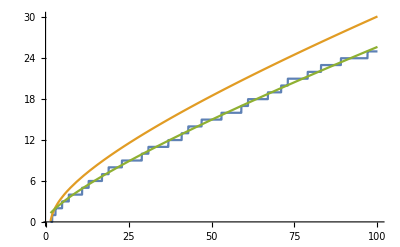

```mathematica
Plot[{PrimePi[x],LogIntegral[x],RiemannR[x]},{x,1.5,100}]
```

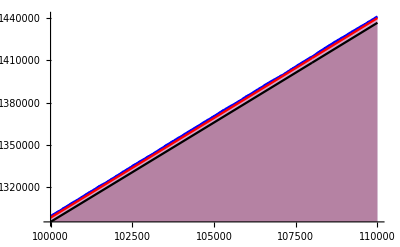

```mathematica
DiscretePlot[{Prime[n],n(Log[n]+Log[Log[n]]-1),n(Log[n]+Log[Log[n]]-1+(Log[Log[n]]-2)/Log[n]-((Log[Log[n]])^2-6Log[Log[n]]+11)/(2(Log[n])^2))},{n,100000,110000},PlotStyle->{Blue,Black,Red}]
```

```mathematica
b=500000000;PrimeEstimateTest=IntegerPart[b(Log[b]+Log[Log[b]]-1+(Log[Log[b]]-2)/Log[b]-((Log[Log[b]])^2-6Log[Log[b]]+11)/(2(Log[b])^2))];
```

```mathematica
NEstimateTest=PrimePi[PrimeEstimateTest]
RelativeError=N[(NEstimateTest-b)/b]
```

500002357

4.714×10^-6

```mathematica
(*This tells us that the approximating function here gives a value too high for Subscript[P, b]. Therefore we must attempt to lower the output in a recursive way until the fucntion settles *)
```

```mathematica
NewNEstimate=b-(NEstimateTest-b)
```

809997542911

```mathematica
NEstimateTest=EstimateChecker[NewNEstimate]
```

810000000000

```mathematica
NewNEstimate=NewNEstimate+(b-NEstimateTest)/2
```

809997543548

```mathematica
1619994471673/2.
```

8.09997×10^11

```mathematica
IntegerPart[999995391/2]
```

499997695

```mathematica
IntegerPart[NEstimateTest(Log[NEstimateTest]+Log[Log[NEstimateTest]]-1+(Log[Log[NEstimateTest]]-2)/Log[NEstimateTest]-((Log[Log[NEstimateTest]])^2-6Log[Log[NEstimateTest]]+11)/(2(Log[NEstimateTest])^2))]]
```

500002310

```mathematica
b=810000000000;
PrimeApprox[x_]:=(IntegerPart[x(Log[x]+Log[Log[x]]-1+(Log[Log[x]]-2)/Log[x]-((Log[Log[x]])^2-6Log[Log[x]]+11)/(2(Log[x])^2))]
);
```

```mathematica
NEstimateTest=EstimateChecker[b];
NewNEstimate=b-(NEstimateTest-b);

PrimeEstimate=PrimeApprox[NewNEstimate];
While[NEstimateTest≠b,
If[Abs[(NEstimateTest-b)/b]>10^-9||Abs[NEstimateTest-b]>10,
NewNEstimate=NewNEstimate-(NEstimateTest-b);,
NewNEstimate=NewNEstimate-(NEstimateTest-b)/10;
];
PrimeEstimate=PrimeApprox[NewNEstimate];
NEstimateTest=PrimePi[PrimeEstimate];
];
PrimeEstimate
```

24120113126984

```mathematica
PrimePi[11037271757]
```

500000000

```mathematica
PrimeApprox[x_]:=(IntegerPart[x(Log[x]+Log[Log[x]]-1+(Log[Log[x]]-2)/Log[x]-((Log[Log[x]])^2-6Log[Log[x]]+11)/(2(Log[x])^2))]
);

NewPrime[n_]:=(
(*Thought process: We need to estimate Subscript[P, n] using an approximation, call it Subscript[P̃, n], calculate PrimePi[Subscript[P̃, n]] and calculate how much our estimate of n is off by. We need to then calculate an adjusted estimate for Subscript[P, n]. The direction in which NEstimate is off will tell us whether to increase or decrease the n used in the prime estimator. We iterate this process until NEstimate=n. Then we scan the odd numbers down from the prime estimate corresponding to the correct n value until PrimePi changes. The number before which it changes is our prime.*)


(*Use a reasonably precise estimate for Subscript[P, n]*)

PrimeEstimate=PrimeApprox[n];
NEstimateTest=PrimePi[PrimeEstimate];NewNEstimate=n-(NEstimateTest-n);
CycleOffset=True;
NoCycleDetected=True;
NEstimateTestArray={};

While[NEstimateTest≠n&&NoCycleDetected,
If[Abs[(NEstimateTest-n)/n]>10^-12||Abs[NEstimateTest-n]>5,
NewNEstimate=NewNEstimate-(NEstimateTest-n);,
NewNEstimate=NewNEstimate-(NEstimateTest-n)/10;
];

PrimeEstimate=PrimeApprox[NewNEstimate];
NEstimateTest=PrimePi[PrimeEstimate];
If[MemberQ[NEstimateTestArray,NEstimateTest]&&NEstimateTest>n,
NoCycleDetected=False;];
NEstimateTestArray=Prepend[NEstimateTestArray,NEstimateTest];

];

If[EvenQ[PrimeEstimate],
PrimeEstimate=PrimeEstimate-1;];
While[PrimePi[PrimeEstimate-2]≥n,
PrimeEstimate=PrimeEstimate-2;
];

PrimeEstimate
);
```

```mathematica
b=1500000000000;
Timing[NewPrime[b]]
Timing[Prime[b*12/10]]
```

{181.648,45624190113149}

{0.,55088764206233}

```mathematica
b=1400000000000;
Timing[NewPrime[b]]
Timing[Prime[b*14/10]]
```

{74.1629,42482567965289}

{31.1846,60158302816223}

```mathematica
Beep[]
```

```mathematica
Timing[Prime[1008000000010]]
```

{19.0633,30244513361819}

```mathematica
b=500000000000;
NEstimateTest=PrimePi[PrimeApprox[b]];NewNEstimate=b-(NEstimateTest-b);
PrimeEstimate=PrimeApprox[b];
CycleOffset=True;
NoCycle=True;
```

```mathematica
If[Abs[(NEstimateTest-b)/b]>10^-12||Abs[NEstimateTest-b]>5,
NewNEstimate=NewNEstimate-(NEstimateTest-b);,
NewNEstimate=NewNEstimate-(NEstimateTest-b)/10;
];
PrimeEstimate=PrimeApprox[NewNEstimate];
NEstimateTest=PrimePi[PrimeEstimate];

If[NEstimateTest==StoredNEstimate&&NEstimateTest>b,
NoCycle=False;];
If[CycleOffset,
CycleOffset=False;
StoredNEstimate=NEstimateTest;,
CycleOffset=True;];
PrimeEstimate
NEstimateTest
StoredNEstimate
NoCycle
CycleOffset
```

14638944639799

500000000005

500000000005

False

False

14638944639799

500000000005

```mathematica
b=500000000000;
NEstimateTest=PrimePi[PrimeApprox[b]];NewNEstimate=b-(NEstimateTest-b);
PrimeEstimate=PrimeApprox[b];
CycleOffset=True;
NoCycle=True;
While[NEstimateTest≠b&&NoCycle,
If[Abs[(NEstimateTest-b)/b]>10^-12||Abs[NEstimateTest-b]>5,
NewNEstimate=NewNEstimate-(NEstimateTest-b);,
NewNEstimate=NewNEstimate-(NEstimateTest-b)/10;
];
PrimeEstimate=PrimeApprox[NewNEstimate];
NEstimateTest=PrimePi[PrimeEstimate];
If[NEstimateTest==StoredNEstimate&&NEstimateTest>b,
NoCycle=False;];
If[CycleOffset,
CycleOffset=False;
StoredNEstimate=NEstimateTest;,
CycleOffset=True;];
];
If[EvenQ[PrimeEstimate],
PrimeEstimate=PrimeEstimate-1;];
While[PrimePi[PrimeEstimate-2]≥b,
PrimeEstimate=PrimeEstimate-2;
];

PrimeEstimate
Prime[b]
```

14638944639703

14638944639703

```mathematica
(*Once the PrimeEstimate gives the n fed to the function, we know we are greater than or equal to the nth prime. We decrement by two until it is no longer equal.*)


PrimeEstimate
Prime[b]
```

7368787

7368787

```mathematica
PrimeEstimate
```

32

```mathematica
Timing[NewPrime[10]]
```

$Aborted

```mathematica
Timing[NewPrime[500000]]
```

$Aborted

```mathematica
Timing[Prime[600000]]
```

{20.9353,33415796732441}

```mathematica
Timing[NewPrime[1500000000000]]
Beep[]
```

$Aborted

```mathematica
Timing[Prime[1500000000000]]
Beep[]
```

{26.5202,45624190113149}

```mathematica
Timing[Prime[810000000000]]
Timing[NewPrime[810000000000]]
```

```mathematica
PrimeApprox=Compile[{{x,_Real}},(IntegerPart[x(Log[x]+Log[Log[x]]-1+(Log[Log[x]]-2)/Log[x]-((Log[Log[x]])^2-6Log[Log[x]]+11)/(2(Log[x])^2))])];
```

```mathematica
b=1500000000000;
PrimeEstimate=PrimeApprox[b]
NEstimateTest=PrimePi[PrimeEstimate]
NewNEstimate=b-(NEstimateTest-b)
NoCycleDetected=True;
NEstimateTestArray={NEstimateTest}
```

45624319925998

1500004129815

1499995870185

{1500004129815}

```mathematica
If[Abs[(NEstimateTest-b)/b]>10^-12||Abs[NEstimateTest-b]>10,
NewNEstimate=NewNEstimate-(NEstimateTest-b);,
NewNEstimate=NewNEstimate-(NEstimateTest-b)/10;
];

PrimeEstimate=PrimeApprox[NewNEstimate]
NEstimateTest=PrimePi[PrimeEstimate]

If[(MemberQ[NEstimateTestArray,NEstimateTest](*||(0<NEstimateTest-b<5)*))&&NEstimateTest>b,
NoCycleDetected=False;];
NEstimateTestArray=Prepend[NEstimateTestArray,NEstimateTest]
```

45624190113180

1500000000001

{1500000000001,1500000000002,1500000000491,1499995867269,1500004129815}

```mathematica
Prime[1500000000000]

Prime[1500000000491]
```

45624190113149

45624190128631

```mathematica
If[EvenQ[PrimeEstimate],
PrimeEstimate=PrimeEstimate-1;];
While[PrimePi[PrimeEstimate-2]≥b,
PrimeEstimate=PrimeEstimate-2];
```

```mathematica
Timing[NewPrime[500000004003]]
```

{35.1938,14638944764287}

```mathematica
Timing[Prime[499001576249]]
```

{11.7157,14608678925171}

```mathematica
Timing[NewPrime[900000004003]]
```

{52.9311,26898370354591}

```mathematica
Timing[Prime[899001576249]]
```

{17.5813,26867497262959}